```mathematica
F[x_]:=c x - Log[Abs[b-a x]]
```

```mathematica
F'[x]
```

c+(a Abs'[b-a x])/Abs[b-a x]

```mathematica
Table[0+eps*0.5,{eps,0,1,.2}]
```

{0.,0.1,0.2,0.3,0.4,0.5}

```mathematica
Total[Flatten[timeh]]
```

4042.91

```mathematica
names={"Backtrack","fminunc","cvx","Exact_line"};
times={Total[Flatten[timeh]]/(16*25000),1658.97/2300,136.11/5,21073.323570/200};
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/poincare/Dropbox/Documentos/DMKM/01 Lyon/Courseware/Op/03

```mathematica
fs=-226894;
d2=Import["fminund.csv"];
```

```mathematica
d3=Import["fhh.mat"];
d3=d3[[1]];
```

```mathematica
d4=Flatten[Import["fhe.mat"]];
```

```mathematica
timeh=Import["timeh.mat"];
timeh=timeh[[1]];
```

```mathematica
Table[Re[d3[[i,1000,j]]]-fs,{i,1,4},{j,1,4}]//TableForm
```

141793. | 141507. | 143143. | 143128.
136787. | 139657. | 145593. | 139171.
133516. | 139418. | 141719. | 141083.
139945. | 135487. | 142401. | 139771.

```mathematica
Table[Re[d3[[i,25000,j]]]-fs,{i,1,4},{j,1,4}]//TableForm
```

25951.7 | 28056.6 | 26992.6 | 26800.5
24956.9 | 25620.1 | 27878.6 | 26872.5
25415.1 | 26492. | 26568.1 | 25617.6
24500.2 | 25660.9 | 26864.7 | 24569.6

```mathematica
mindest=Min[Flatten[Table[{Re[d3[[i,25000,j]]]-fs},{i,1,4},{j,1,4}]]]
stddest=StandardDeviation[Flatten[Table[{Re[d3[[i,25000,j]]]-fs},{i,1,4},{j,1,4}]]]
```

24500.2

1067.59

```mathematica
Table[{(Re[d3[[i,25000,j]]]-fs-(mindest))/stddest},{i,1,4},{j,1,4}]//TableForm
```

1.35966 | 3.33131 | 2.33463 | 2.15473
0.427785 | 1.04903 | 3.16452 | 2.22215
0.856989 | 1.86572 | 1.93702 | 1.04666
0. | 1.08724 | 2.21486 | 0.0650455

```mathematica
BubbleChart[Table[{i*.2,j*.1,(Re[d3[[i,25000,j]]]-fs-(mindest)+1)/stddest},{i,1,4},{j,1,4}]]
```

-Graphics-

```mathematica
Dimensions[Flatten[Table[Table[Re[d3[[i,All,j]]],{i,1,4}],{j,1,4}],1]]
```

{16,25000}

```mathematica
alpha={0.1,0.2,0.3,0.4}; beta={0.2,0.4,0.6,0.8};
```

```mathematica
labels1=Flatten[Table[ToString[{alpha[[i]],beta[[j]]}],{i,1,4},{j,1,4}],1]
```

{{0.1, 0.2},{0.1, 0.4},{0.1, 0.6},{0.1, 0.8},{0.2, 0.2},{0.2, 0.4},{0.2, 0.6},{0.2, 0.8},{0.3, 0.2},{0.3, 0.4},{0.3, 0.6},{0.3, 0.8},{0.4, 0.2},{0.4, 0.4},{0.4, 0.6},{0.4, 0.8}}

```mathematica
f3=ListLogLogPlot[Flatten[Table[Table[Re[d3[[i,All,j]]],{i,1,4}],{j,1,4}],1]-fs,Joined->True,PlotLegends->Placed[labels1,Below],AxesLabel->{"Iteration","Log_10|f(x_i)-p^*|"}];
```

```mathematica
Export["f3.png",f3]
```

f3.png

```mathematica
d2[[All,2]]=d2[[All,2]]-fs;
```

```mathematica
Re[d3[[1,All,4]]]
```

{22876.8,-29258.4,-29673.6,-29756.4,-29839.1,-29921.6,-30003.9,-30086.1,-32135.5,-32136.4,-32141.1,-34175.6,-34591.2,24974,-200081.,-200083.,-200084.,-200084.,-200086.,-200087.,-200087.,-200089.,-200089.,-200090.,-200092.,-200092.,-200093.}
 |  |  |  |

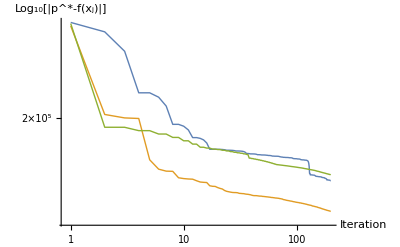

```mathematica
ListLogLogPlot[{d2[[1;;200,2]],Re[d3[[4,1;;200,1]]]-fs,DeleteCases[d4,0.]-fs},Joined->True,PlotRange->All,PlotStyle->Thick,AxesLabel->{"Iteration","Log_10[|p^*-f(x_j)|]"}]
```

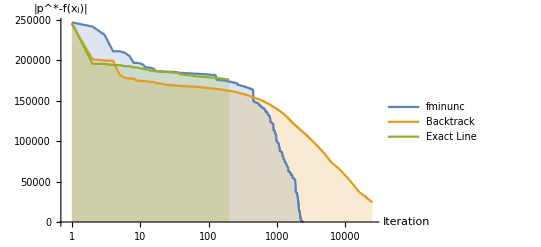

```mathematica
f6=ListLogLinearPlot[{d2[[All,2]],Re[d3[[4,All,1]]]-fs,DeleteCases[d4,0.]-fs},Joined->True,PlotRange->All,AxesLabel->{"Iteration","|p^*-f(x_j)|"},Filling->Axis,PlotLegends->Placed[{"fminunc","Backtrack","Exact Line"},Below]]
```

```mathematica
Export["f6.png",f6]
```

f6.png

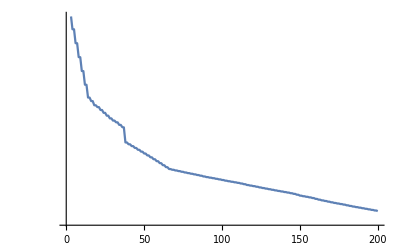

```mathematica
ListLogPlot[DeleteCases[d4,0.]-fs,Joined->True]
```

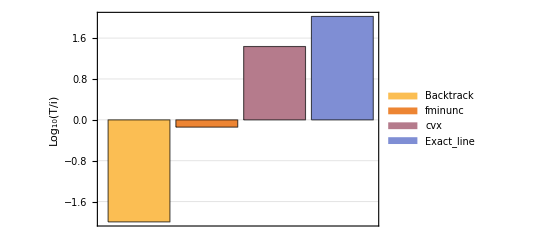

```mathematica
f1=BarChart[{Log[10,times]},ChartLegends->Placed[names,Below],FrameLabel->{"",Subscript[Log, 10][T/i]},PlotTheme->"Detailed"]
```

```mathematica
Export["f1.eps",f1]
```

f1.eps

```mathematica
TableForm@timeh
```

159.5 | 178.859 | 212.064 | 301.382
174.958 | 210.879 | 238.223 | 301.572
173.427 | 187.241 | 239.001 | 423.122
239.208 | 280.326 | 349.272 | 373.878

```mathematica
f5=Show[{ArrayPlot[Table[timeh[[j,5-i]],{i,1,4},{j,1,4}],ColorFunction->"TemperatureMap",PlotLegends->Automatic],BubbleChart[Table[{-.5+j,-.5+i,(Re[d3[[i,25000,j]]]-fs-(mindest)+1)/stddest},{i,1,4},{j,1,4}]]},FrameLabel->{Subscript[α, i],Subscript[β, j]},FrameTicks->Automatic,Frame->True]
```

-Graphics-

```mathematica
Export["f5.eps",f5]
```

f5.eps

```mathematica
Flatten[Table[{Re[d3[[i,25000,j]]]-fs},{i,1,4},{j,1,4}]]
```

{25951.7,28056.6,26992.6,26800.5,24956.9,25620.1,27878.6,26872.5,25415.1,26492.,26568.1,25617.6,24500.2,25660.9,26864.7,24569.6}

```mathematica
Max[Flatten[Table[{Re[d3[[i,25000,j]]]-fs},{i,1,4},{j,1,4}]]]
Min[Flatten[Table[{Re[d3[[i,25000,j]]]-fs},{i,1,4},{j,1,4}]]]
```

28056.6

24500.2

```mathematica
Log[10,%]
```

3.55102

```mathematica
Log[10,Flatten[Table[{Re[d3[[i,25000,j]]]-fs},{i,1,4},{j,1,4}]]]
```

{4.41417,4.44804,4.43124,4.42814,4.39719,4.40858,4.44527,4.42931,4.40509,4.42311,4.42436,4.40854,4.38917,4.40927,4.42918,4.3904}

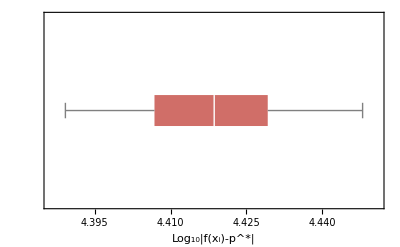

```mathematica
f4=BoxWhiskerChart[Log[10,Flatten[Table[{Re[d3[[i,25000,j]]]-fs},{i,1,4},{j,1,4}]]],BarOrigin->Left,ChartStyle->56,FrameLabel->{"Log_10|f(x_i)-p^*|",""}]
```

```mathematica
10^0.0689
```

1.17193

```mathematica
Export["f4.eps",f4]
```

f4.eps

```mathematica
BubbleChart[Table[{i,j,Re[d3[[i,25000,j]]]-fs-24000},{i,1,4},{j,1,4}]]
```

-Graphics-

```mathematica
Table[{Re[d3[[i,25000,j]]]-fs-24000,timeh[[j,i]]},{i,1,4},{j,1,4}]//TableForm
```

1951.72
159.5 | 4056.64
174.958 | 2992.59
173.427 | 2800.53
239.208
956.86
178.859 | 1620.1
210.879 | 3878.58
187.241 | 2872.5
280.326
1415.07
212.064 | 2491.98
238.223 | 2568.11
239.001 | 1617.56
349.272
500.161
301.382 | 1660.89
301.572 | 2864.72
423.122 | 569.603
373.878

```mathematica
Table[{Re[d3[[i,189,j]]]-fs},{i,1,4},{j,1,4}]//TableForm
```

168076. | 163575. | 163548. | 163997.
156860. | 165082. | 170157. | 161686.
154050. | 168165. | 174017. | 164952.
162774. | 155867. | 162680. | 160721.

```mathematica
-5.0360*10^4-fs
```

176534.

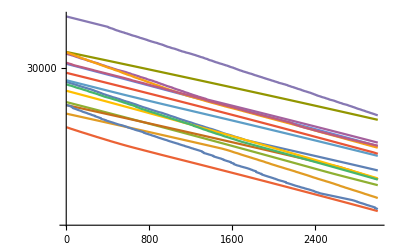

```mathematica
ListLogPlot[Flatten[Table[Table[Re[d3[[i,22000;;25000,j]]],{i,1,4}],{j,1,4}],1]-fs,Joined->True]
```

```mathematica
Min[Flatten[Table[Re[d3[[i,25000,j]]],{i,1,4},{j,1,4}]]]
```

-202394.

```mathematica
final={Min[Flatten[Table[Re[d3[[i,25000,j]]],{i,1,4},{j,1,4}]]],-226885,-226894,Min[Re[d4]]}-fs
```

{24500.2,9,0,176211.}

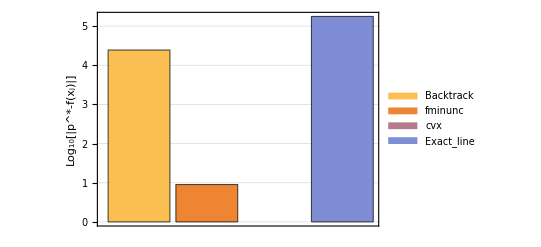

```mathematica
f2=BarChart[{Log[10,final]},ChartLegends->Placed[names,Below],FrameLabel->{"","Log_10[|p^*-f(x_j)|]"},PlotTheme->"Detailed"]
```

```mathematica
Export["f2.eps",f2]
```

f2.eps